```mathematica
Offpaclet:ref/Off[General::munfl];
Offpaclet:ref/Off[General::stop];
```

```mathematica
LCD={{2.00,1.0,-142.364,-106.2793,68.488},{4.00,1.0,-505.164,-434.9584,677.799},{6.00,1.0,-1090.584,-986.2518,2652.651},{8.00,1.0,-1898.622,-1760.1617,7816.228},{10.0,1.0,-2929.277,-2756.6884,20483.217},{12.0,1.0,-4182.363,-3975.6195,50939.941},{15.0,1.0,-6479.576,-6221.5028,195570.801}};
```

## Solvers

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
alpha[r_,k_,l_,h_]:=(1+h (D[FunctionExpand[RiccatiBesselN[k x,l]],x]/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
beta[r_,k_,l_,h_]:=h FunctionExpand[RiccatiBesselJ[k r,l]](((D[FunctionExpand[RiccatiBesselJ[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselJ[k r,l]])-((D[FunctionExpand[RiccatiBesselN[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
```

```mathematica
SolveSecularNL0[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ]:=Block[{p,RRmax,nnGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,Tere,fit,nn,δ,L,r,mod,usol},
p=momentum;
RRmax=Rdis;
nnGrid=Npoints;
hDif=RRmax/nnGrid;
L=Lin;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nnGrid,nnGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 (p^2-mh2 V0[i hDif])+(L(L+1))/i^2,{i,1,nnGrid}]];
Wmat=Table[-hDif^3 mh2 W[i hDif,j hDif,p],{i,1,nnGrid},{j,1,nnGrid}]; 

If[p==0,

bcol=Table[Which[i==nnGrid,-hDif,1==1,0],{i,1,nnGrid}];
Dmat⟦nnGrid⟧⟦nnGrid⟧+=1; (*this is only for 0 energy*)

ucol=Array[Subscript["u", ##]&,{nnGrid}];
Amat=Dmat+Wmat+Kmat;
ddmat=Dmat;
wwmat=Wmat;
kkmat=Kmat;
aamat=Amat;
bbvec=bcol;

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];
Tere=RRmax-usol⟦-1⟧;
,

bcol=ConstantArray[0,nnGrid];
ucol=Array[Subscript["u", ##]&,{nnGrid}];
Amat=Dmat+Wmat+Kmat;
bcol⟦-1⟧=- hDif p(Cos[p RRmax]+Sin[p RRmax]Tan[p RRmax]);
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1-hDif p Tan[p Rmax];

usol=LinearSolve[Amat,bcol];
ddmat=Dmat;
wwmat=Wmat;
kkmat=Kmat;
aamat=Amat;
bbvec=bcol;

wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];
Tere=p^(2L+1) ((usol⟦-1⟧-Sin[p RRmax])/Cos[p RRmax])^-1;
];

{Tere,wf}
]
```

```mathematica
SolveSecularNL1[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ]:=Block[{p,RRmax,nnGrid,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,asywf,wf,wffree,tanDelta,fit,nn,δ,L,r,mod,usol,lam,lec},
p=momentum;
RRmax=Rdis;
nnGrid=Npoints;
hDif=RRmax/nnGrid;
L=Lin;

(* Matrix components *)
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{nnGrid,nnGrid}];
Dmat=DiagonalMatrix[Table[hDif^2 (p^2-mh2 V0[i hDif]-(L(L+1))/(i hDif)^2),{i,1,nnGrid}]];
Wmat=Table[-hDif^3 mh2 W[i hDif,j hDif,p],{i,1,nnGrid},{j,1,nnGrid}]; 

bcol=ConstantArray[0,nnGrid];
ucol=Array[Subscript["u", ##]&,{nnGrid}];
Amat=Dmat+Wmat+Kmat;

If[p==0,
(* ------------------------- zer0 momentum ------------------------- *)

If[L==0,
bcol⟦-1⟧=- hDif;
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1
,
bcol[[-1]]=1-1./nnGrid;
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+hDif^2 nnGrid;
];

usol=LinearSolve[Amat,bcol];
wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];

If[L==0,
tanDelta=RRmax-usol⟦-1⟧;
,
tanDelta=RRmax^3/3-usol⟦-1⟧ RRmax;
tanDelta=RRmax-usol⟦-1⟧;
];
,
(* ------------------------- non-zer0 momentum --------------------- *)

(*bcol⟦-1⟧=- hDif p(Cos[p RRmax]+Sin[p RRmax]Tan[p RRmax]);*)
bcol⟦-1⟧=- beta[RRmax,p,L,hDif];
(*Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+1-hDif p Tan[p RRmax];*)
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[RRmax,p,L,hDif];

usol=LinearSolve[Amat,bcol];

wf=Table[{i hDif,usol⟦i⟧},{i,1,nnGrid}];
tanDelta= (RiccatiBesselJ[p RRmax,L]/RiccatiBesselN[p RRmax,L])-(usol⟦-1⟧/RiccatiBesselN[p RRmax,L]);
];

{tanDelta,wf}
]
```

```mathematica
Scatt1[α0_?NumberQ]:=Block[{f,w},
c0=α0;
(* 1/2 is to have μ instead of m*)
f=Replace[w,NDSolve[{w'[r]+w[r]^2- mh2 Vα0[α0,r]==0,w[0]==10^40},w,{r,0,R}]⟦1,1⟧];R-f[R]^-1]
```

## Solve

```mathematica
m=938.92;
Lrel=1;
```

General::munfl: (7.38603×10^-305)/6400 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.891] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.12088×10^-306)/6400 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.36896×10^-306)/6400 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-713.892] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-709.267] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.873] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.855] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-708.574] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.749] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.051] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-709.083] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.041] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.869] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

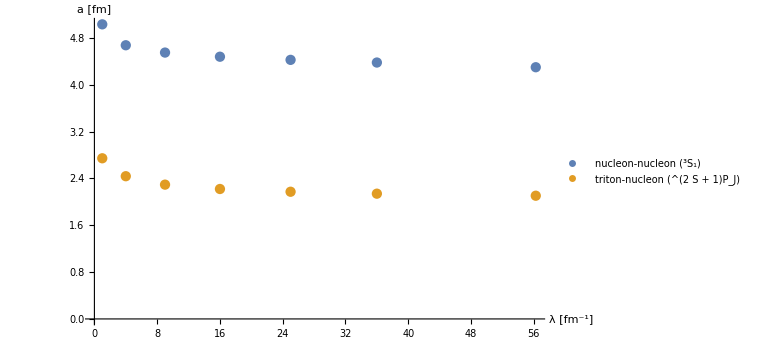

```mathematica
Λl=√(4 Transpose[LCD]⟦1⟧);
αl=Transpose[LCD]⟦2⟧;
C0l=Transpose[LCD]⟦3⟧;
D0l=Transpose[LCD]⟦4⟧;
data={};
SetSharedVariable[data];
ParallelDo[{
Λ=Λl⟦j⟧;
λ=0.25 (Transpose[LCD]⟦1⟧⟦j⟧)^2;
α=αl⟦j⟧;
C0=C0l⟦j⟧;
D0=D0l⟦j⟧;

(*Calculate fermion fermion*)
μ1=m/2;hbar=197.327053;mh2=(2 μ1)/(hbar)^2;
V0[r_]                   := C0  Exp[- λ r^2];
Vα0[Cc_,r_]       :=Cc  ⅇ^(-λ r^2);
W[r_,rp_,e_]  :=0;

nGrid     =400;
R             =5;
aff=SolveSecularNL1[R,nGrid,0.0,0]⟦1⟧;

(* Trimer - Dimer case^4 H *)
μ1=3/2 μ;hbar=197.327053;mh2=(2 μ1)/(hbar)^2;
η2=2 C0((3α)/(3α+λ))^(3/2);η3=8D0((3 α^2)/(12 α^2+16α λ+λ^2))^(3/2);
ω2=(3 α λ)/(3α+λ);ω3=(12α λ(α+λ))/(12 α^2+16α λ+λ^2);
ξ1=27/8(3/2 α)^(3/2)mh2^-1;ξ2=-2 27 (3/2 α)^(3/2)C0(α/(4α+λ))^(3/2);ξ3=-27(3/2 α)^(3/2)D0(α/(4α+5 λ))^(3/2);

a1=15/16 α;a2=(3α(5α+8λ))/(4(4α+λ));a3=(3(20 α^2+52α λ+27 λ^2))/(4(16α+20λ));
b1=18/16 α;b2=(9α(α+λ))/(2(4α+λ));b3=(9(4 α^2+8α λ+3 λ^2))/(2(16α+20λ));
c1=15/16 α;c2=(3α(5α+2λ))/(4(4α+λ));c3=(3(20 α^2+28α λ+3 λ^2))/(4(16α+20λ));


V0[r_]:=η2 ⅇ^(-ω2  r^2)+η3 ⅇ^(-ω3  r^2);
W[r_,rp_,p_]:=Re[-(r rp 4 π)(ξ1  ⅇ^(-a1 r^2- c1 rp^2) ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+2/r^2-p^2) ⅈ SphericalBesselJ[1,ⅈ b1 r rp]-4 a1 b1 r rp (SphericalBesselJ[0,ⅈ b1 r rp]/Sqrt[3]
-SphericalBesselJ[2,ⅈ b1 r rp] 2/Sqrt[15]))+ξ2 ⅈ SphericalBesselJ[1,ⅈ b2 r rp] ⅇ^(-a2 r^2- c2 rp^2)+ ξ3 ⅈ SphericalBesselJ[1,ⅈ b3 r rp] ⅇ^(-a3 r^2- c3 rp^2))];

nGrid=300;
Rmax=8;
Pp={0.001};(*,0.002,0.003,0.004,0.005,0.007,0.008,0.009,0.01,0.02};*)

Do[
TanD=SolveSecularNL1[Rmax,nGrid,Pp⟦i⟧,Lrel]⟦1⟧;
atf=-TanD/Pp[[i]]^(2 Lrel+1);
,{i,Range[Length[Pp]]}
];


AppendTo[data,{λ,aff,atf}];
(*Print["λ = ",λ,"   FD/VARP Methods: a_ff = ", aff," / ", Scatt1[C0]];*)

},{j,1,Length[Λl]}];
ListPlot[{data[[All,1;;2]],data[[All,{1,3}]]},PlotLegends->{Style["nucleon-nucleon (^3S_1)",18],Style["triton-nucleon (^(2  S + 1)P_J)",18]},ImageSize->Large,AxesLabel->{Style["λ [fm^-1]",20],Style["a [fm]",20]}]
```

```mathematica
ClearAll;
μ=2 m/3;hbar=197.327053;mh2=(2 μ)/(hbar)^2;
η2[C_,λ_,α_]:=2 C((3α)/(3α+λ))^(3/2); η3[D_,λ_,α_]:=8D((3 α^2)/(12 α^2+16α λ+λ^2))^(3/2);
ω2[λ_,α_]:=(3 α λ)/(3α+λ); ω3[λ_,α_]:=(12α λ(α+λ))/(12 α^2+16α λ+λ^2);
ξ1[λ_,α_]:=27/8 (3/2 α)^(3/2)mh2^-1;ξ2[C_,λ_,α_]:=-2 27 (3/2 α)^(3/2)C(α/(4α+λ))^(3/2);ξ3[D_,λ_,α_]:=-27(3/2 α)^(3/2)D(α/(4α+5 λ))^(3/2);

a1[α_]:=15/16 α;a2[λ_,α_]:=(3α(5α+8λ))/(4(4α+λ));a3[λ_,α_]:=(3(20 α^2+52α λ+27 λ^2))/(4(16α+20λ));
b1[α_]:=18/16 α;b2[λ_,α_]:=(9α(α+λ))/(2(4α+λ));b3[λ_,α_]:=(9(4 α^2+8α λ+3 λ^2))/(2(16α+20λ));
c1[α_]:=15/16 α;c2[λ_,α_]:=(3α(5α+2λ))/(4(4α+λ));c3[λ_,α_]:=(3(20 α^2+28α λ+3 λ^2))/(4(16α+20λ));



V0[r_,C_,D_,λ_,α_]:=η2[C,λ,α] ⅇ^(-ω2[λ,α]  r^2)+η3[D,λ,α] ⅇ^(-ω3[λ,α] r^2);
W[r_,rp_,p_,C_,D_,λ_,α_]:=Re[-(r rp 4 π)(ξ1[λ,α]  ⅇ^(-a1[α] r^2- c1[α] rp^2) ((-(4 a1[α]^2 r^2+b1[α]^2 rp^2-2 a1[α])+2/r^2-p^2) I SphericalBesselJ[1,ⅈ b1[α] r rp]-4 a1[α] b1[α] r rp (SphericalBesselJ[0,ⅈ b1[α] r rp]/Sqrt[3]
-SphericalBesselJ[2,ⅈ b1[α] r rp] 2/Sqrt[15]))-ξ2[C,λ,α] ⅈ SphericalBesselJ[1,ⅈ b2[λ,α] r rp] ⅇ^(-a2[λ,α] r^2- c2[λ,α] rp^2)-ξ3[D,λ,α] ⅈ SphericalBesselJ[1,ⅈ b3[λ,α] r rp] ⅇ^(-a3[λ,α] r^2- c3[λ,α] rp^2))];

cc=LCD[[6]][[3]];
dd=LCD[[6]][[5]];
ll=0.25 LCD[[6]][[1]]^2;
ll=LCD[[6]][[1]];
aa=LCD[[6]][[2]];
Print["Λ = ", 4 Sqrt[ll]," fm^-1      α = ",aa," fm^-2       C0 = ", cc,  " MeV        D0 = ",dd," MeV" ];
Plot3D[W[r,rp,0.5,cc,dd,ll,aa],{r,0,4},{rp,0,4},PlotRange->Full,AxesLabel->Automatic,PlotRange->{Automatic,Automatic,{-500,200}},ImageSize->Large]

Animate[Show[Plot[W[x,x,0.5,cc,dd,ll,sc aa],{x,0,5},PlotRange->Full,ImageSize->Large,PlotLegends->{"V_(non - local)"},PlotStyle->Red],
Plot[V0[x,cc,dd,ll,sc aa],{x,0,20},PlotRange->Full,ImageSize->Large,PlotLegends->{"V_local"},PlotStyle->Blue]],{sc,1.1,0.5},AnimationRunning->False]
```

Λ = 13.8564 fm^-1      α = 1. fm^-2       C0 = -4182.36 MeV        D0 = 50939.9 MeV

-Graphics3D-

```mathematica
η2[cc,ll,aa]

ξ2[cc,ll,aa]
1/mh2
ξ1[ll,aa]
(-(4 a1[aa]^2 r^2+b1[aa]^2 rp^2-2 a1[aa])+2/r^2-p^2)/.{r->2,rp->2,p->0}
```

-178.458

1640.07

31.1033

192.849

-16.75

```mathematica
FunctionExpand[SphericalBesselJ[0,rp]]
```

Sin[rp]/rp

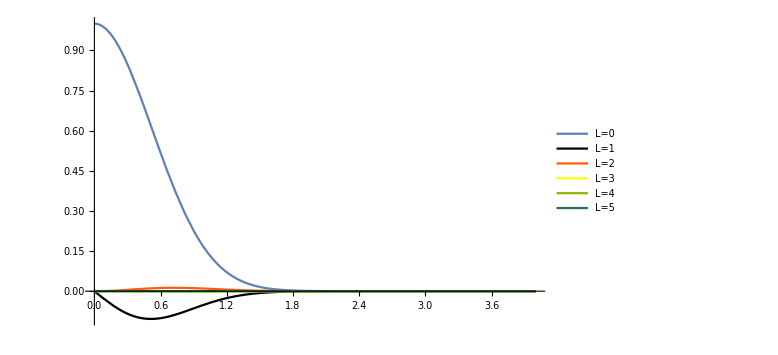

```mathematica
Show[Plot[I^# Exp[-2 r^2] FunctionExpand[SphericalBesselJ[#,I r]],{r,0,4},PlotRange->Full,PlotStyle->{ColorData[3,"ColorList"][[#]]},PlotLegends->{"L="<>ToString[#]},ImageSize->Large]&/@Range[0,5],PlotRange->All]
```